## things to play around with: TList scale nCutoff Ttrap, frad, fax note, for third data set I set scale to 0.8 manually

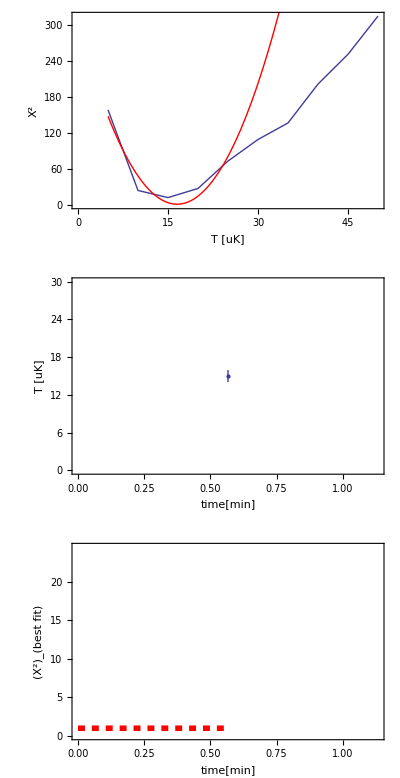

nbar=3.6873+/-0.268262

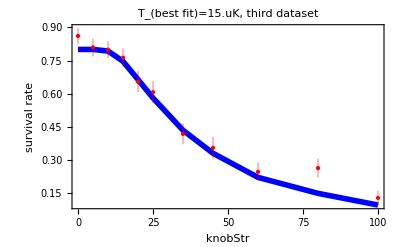

```mathematica
Clear["Global`*"]
Needs["ErrorBarLogPlots`"]
data="third";
first="0 0.8750 0.0329
5.0000 0.9198 0.0261
10.0000 0.8053 0.0405
15.0000 0.5350 0.0499
20.0000 0.3287 0.0452
25.0000 0.3692 0.0466
35.0000 0.3889 0.0490
45.0000 0.1535 0.0357
60.0000 0.1106 0.0305
80.0000 0.0722 0.0269
100.0000 0.0469 0.0210";
second="0    0.8786    0.0320
    5.0000    0.8850    0.0317
   10.0000    0.7865    0.0417
   15.0000    0.5735    0.0490
   20.0000    0.4858    0.0485
   25.0000    0.5101    0.0502
   35.0000    0.3032    0.0474
   45.0000    0.2327    0.0420
   60.0000    0.2123    0.0396
   80.0000    0.1449    0.0339
  100.0000    0.0591    0.0240";
third="   0    0.8608    0.0349
    5.0000    0.8093    0.0398
   10.0000    0.7991    0.0378
   15.0000    0.7626    0.0427
   20.0000    0.6546    0.0483
   25.0000    0.6071    0.0493
   35.0000    0.4189    0.0468
   45.0000    0.3557    0.0486
   60.0000    0.2477    0.0417
   80.0000    0.2644    0.0432
  100.0000    0.1298    0.0328";
lala=Switch[data,
"first",first,
"second",second,
"third",third];

survival=ToExpression[
StringSplit[lala
,{" ","\n"}]];
survival=DeleteCases[survival,Null];
survival=Partition[survival,3];
survErr=survival[[;;,3]];
survival=Thread[{survival[[;;,{1,2}]],ErrorBar[#]&/@survErr}];

plot1=ErrorListPlot[survival,Joined->(False),PlotStyle->{Thickness[.001],Red},Axes->False,Frame->True,FrameLabel->{knobStr,"survival rate","mean = "<>ToString[Round[100 Mean[ survival[[;;,1]][[;;,2]]]]]<>"%"},PlotRange->{All,{0,1.1}}];
(*units and constants for trap depth mostly*)
kHz=10^3;
nm=10^-9;
mK=10^-3;
uK=10^-6;
us=10^-6;
kB=1.38064852 10^-23;
ℏ=1.0545718 10^-34;
amu=1.66054 10^-27;
λtrap=970 nm;
m=132.90545 amu;
fitPrev={}; (*store previous fits*)
{Ttrap,frad,fax}={0.67mK,70.7kHz,11.8kHz};
TZERO = AbsoluteTime[];
α=1;
{Ttrap,frad,fax}={α(75/70.7)^2 0.67mK,√α 75kHz,√α 75/70.7 11.8kHz}; 
TList=Range[5,50,5]uK; (*atom temp guesses. assuming: T in uK, and they are in increasing order*)

Utrap = kB Ttrap;
ftrap={frad,frad,fax(*√((λtrap^2 m frad^4)/(2 Utrap))*)} ;

w0=√(Utrap/(ftrap[[1]]^2 m π^2)); (*0.67, 133 amu, 71kHz gives 917 nm*)
w[z_]:=w0√(1+((λtrap z)/(π w0^2))^2);
U[r_]:=Utrap(1-w0^2/w[r[[3]]]^2 Exp[-2 (r[[1]]^2+r[[2]]^2)/w[r[[3]]]^2]);

Δt=Sort[survival[[;;,1]][[;;,1]]] us;
nSim=1000; (*number of realizations*)

scale=.8;Max[survival[[;;,1]][[;;,2]]]; (*maximum survival rate, haven't appended error bars yet*)

mcTOFfit=Reap[
Do[

coordsInit=Reap[
Do[(*loop nSim times*)
coordsInitSingle=Reap[
Do[(*loop over 3 axes*)
nbar=1/(Exp[(ℏ 2π f)/(kB T)]-1);
nCutoff=10Ceiling[nbar];
Pn=Table[nbar^n/(nbar+1)^(n+1),{n,0,nCutoff}]; (*probability distribution*)
Cn=Accumulate[Pn]; (*cumulative distr*)

(*sample n from a probability distribution Pn*)
(*compare random number to cumulative distribution. put 1 if positive, 0 if negative.*)
listpn=Boole[Positive[#]]&/@(RandomReal[]-Cn);
(*the total of this list gives the corresponding n*)
n=Total[listpn];


ϵn=(n+1/2)ℏ 2π f;

(*randomly sample mixing angle b/t v and x*)
(*ie randomly distribute the energy b/t position and velocity. *)
θ=RandomReal[2π];
xtemp=(√ϵn Sin[θ])/(√(1/2 m)(2π f));
vtemp=(√ϵn Cos[θ])/(√(1/2 m)); 

coordstemp={xtemp,vtemp};

Sow[coordstemp],
{f, ftrap}
]
][[2,1]];

(*list of the form {{x,y,z},{vx,vy,vz}}*)
coordsInitSingle=Transpose[coordsInitSingle];
Sow[coordsInitSingle]
,{j,nSim}]
][[2,1]];

rInit=Transpose[coordsInit][[1]];
vInit=Transpose[coordsInit][[2]];
KInit=m/2 Norm[#]^2&/@vInit;

(*sort by realizations. ie each list scans thru all Δt for a single realization*)
rFin=Transpose[rInit+vInit #&/@Δt];
PFin=U[#]&/@#&/@rFin;

EFin=(#1+#2)&[PFin,KInit];
SurvProb=Thread[{Δt/us,scale Total[#]&/@Transpose[Boole[Positive[Utrap-EFin]]]/Length[rInit]}];

sigma=1.Flatten[#&/@survErr];
chiSquare=Total[((SurvProb-survival[[;;,1]])^2)[[;;,2]]/sigma^2];
Sow[{T/uK,SurvProb,chiSquare}]
,{T,TList}]
][[2,1]];

chiSquares=mcTOFfit[[;;,3]];
PosBestFit=Flatten[Position[chiSquares,Min[chiSquares]]];
TBestFit=mcTOFfit[[;;,1]][[PosBestFit]][[1]];

chisquaremin=chiSquares[[PosBestFit]][[1]];
plot1=
Show[
{
ListPlot[mcTOFfit[[PosBestFit,2]][[1]],Joined->True,PlotStyle->{Thickness[.01],Blue},Frame->{True,True},Axes->False,FrameLabel->{knobStr,"survival rate"},PlotRange->All,PlotLabel->"T_(best fit)="<>ToString[Round[TBestFit,.01]]<>"uK, "<>data<>" dataset"],
plot1
}
];
(*list of triplets: {"param name", est val, error.,chisquaremin}*)

fitParams={"T [uK]",TBestFit,chisquareErr,chisquaremin};

(*only append if fit is good. check goodness of fit!!*)
chisquarefitfn=a (x-x0)^2+b;
(*only fit to the min and 2 points on either side*)
chiSquaresNearMin=mcTOFfit[[;;,{1,3}]][[PosBestFit[[1]]-2;;PosBestFit[[1]]+2]]; 

chisquarenlm=NonlinearModelFit[chiSquaresNearMin,chisquarefitfn,{a,{ x0,TBestFit}, {b,chisquaremin}},x];
chisquarefit=chisquarenlm["BestFitParameters"];
chisquareErr=√(( a/.chisquarefit)^-1);(*error taken to be √(2(∂_T ∂_T Χ^2)^-1)from energy distr of single atom... paper*)

If[
Head[chisquarefit]==List&&Positive[2chisquareErr-Abs[x0-TBestFit]/.chisquarefit]&&
And@@(Positive[chisquarenlm["ParameterPValues"]-10^-5])&&
a>0/.chisquarefit,
(*returns True only if 
nlmfit didn't crash 
AND x0_fit is within 2*std error of TBestFit 
AND all P values >10^-5
AND we are sitting at a minimum
*)
AppendTo[fitPrev,{(AbsoluteTime[]-TZERO)/60,fitParams}
]
];

(*plot temp vs time and plot chi square vs time*)
fitTimes=fitPrev[[;;,1]];
fitStr=fitPrev[[1,2,1]];
fitVals=fitPrev[[;;,2]][[;;,2]];
fitErr=fitPrev[[;;,2]][[;;,3]];
fitChiSquare=fitPrev[[;;,2]][[;;,4]];

aa=Thread[{fitTimes,fitVals}];
bb=Thread[{aa,ErrorBar[#]&/@fitErr}];
dd=Thread[{fitTimes,fitChiSquare}];

ee=Show[{
ListPlot[mcTOFfit[[;;,{1,3}]],Joined->True,FrameLabel->{"T [uK]","Χ^2","T_(best fit)="<>ToString[TBestFit]<>"uK"},Frame->True],
Plot[chisquarefitfn/.chisquarefit,{x,Min[TList/uK],Max[TList/uK]},PlotStyle->Red]
}
];
ff=ErrorListPlot[bb,Frame->True,Axes->False,FrameLabel->{"time[min]",fitStr,"last="<>ToString[fitVals[[-1]]]<>"("<>ToString[fitErr[[-1]]]<>")"}];
gg=Show[
{
ListPlot[dd,Frame->True,Axes->False,FrameLabel->{"time[min]","(Χ^2)_(best fit)","last="<>ToString[fitChiSquare[[-1]]]},Joined->True],
Plot[1,{x,0,Max[dd[[;;,1]]]},PlotStyle->{Red, Thickness[.01],Dashed}]

}
];

Print[GraphicsGrid[Partition[{ee,ff,gg},1]]];

(*nbar of radial dir. and error if you have rnr*)

dftrap=1 kHz;
nbar=1/(Exp[(ℏ 2π f)/(kB T)]-1);
Δnbar=√((D[nbar, T])^2(chisquareErr uK)^2+(D[nbar, f])^2(dftrap)^2)/.T->TBestFit uK/.f->frad;
Print["nbar="<>ToString[nbar/.T->TBestFit uK/.f->frad]<>"+/-"<>ToString[Δnbar]];

plot1
```

## save

Part::partw: Part 1 of {} does not exist.

Part::partw: Part -1 of {} does not exist.

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

Part::partw: Part -1 of {} does not exist.

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

Plot::plln: Limiting value -∞ in {x, 0, Max[dd ⟦ 1 ;; All, 1 ⟧]} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[{ListPlot[{}, Frame → True, Axes → False, FrameLabel → {"time[min]", "(\!\(\*SuperscriptBox[\(\[CapitalChi]\), \(2\)]\)\!\(\*SubscriptBox[\()\), \(best\\ fit\)]\)", "last={}[[-1]]"}, Joined → True], Plot[1, {x, 0, Max[dd ⟦ 1 ;; All, 1 ⟧]}, PlotStyle → {Red, Thickness[0.01], Dashed}]}].

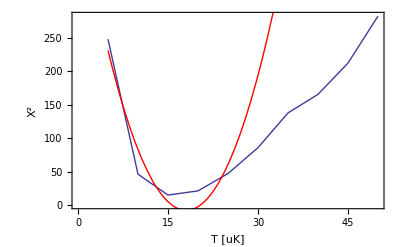

nbar=3.6873+/-0.239351

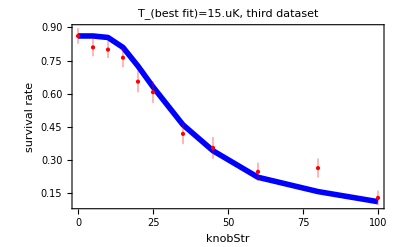

## save

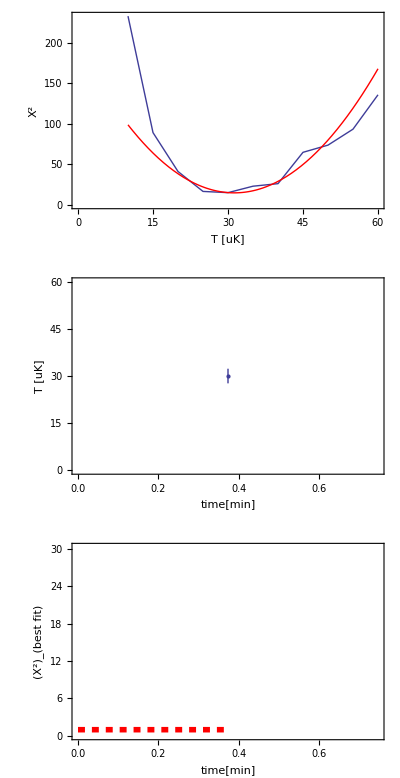

nbar=7.84464+/-0.654324

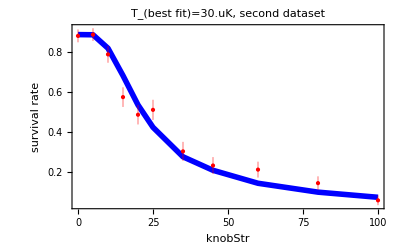

## save

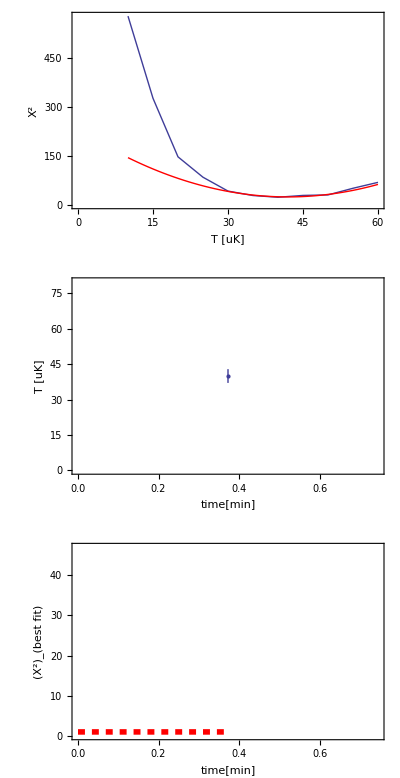

nbar=10.6204+/-0.822925